```mathematica
n=126456119090476383371855906671054993650778797793018127;
e=7937;
cipher={60833078379832053733665235104517667174744887177103669,47845135110330425759238983903835414959478333031403660,29226436027122547212719862444995325439654173683124719,26852073219160460393476539289841435348076003235573562,18536789208272843521201394019815486297145984481554371,60946204295190537657611153931568067486237180585452998,23651682987715782801807742133012602969829495021520007,112630050746349041975951827486336529408641182025699787,46387928110260904731968713144311859620686048715174256,101614383351383083936620333816943396668613455381224570};
```

```mathematica
crackRSA[cipher_, n_, e_]:=Module[{divs,p,q,phi,d,decryptF, extractF,decryptCipher,decryptAscii},
divs=Divisors[n];
p=divs[[2]];
q=divs[[3]];
phi=(p-1)(q-1);
d=PowerMod[e,-1,phi];
decryptF[msg_]:=Return[PowerMod[msg,d,n]];
decryptCipher=decryptF/@cipher;
extractF[msg_]:=Module[{m=msg,localStore={}},
While[m≠0,AppendTo[localStore,Mod[m, 256]];m=Quotient[m, 256]];
Return[localStore];
m
];
decryptAscii=extractF/@decryptCipher;
Return[FromCharacterCode[Flatten[decryptAscii]]];
];
```

```mathematica
crackRSA[cipher, n, e]
```

Congratulations! You have now managed to crack the RSA cipher. This means that you have a pass grade for project 2. If you want to pursue a higher grade you need to solve one more problem.

```mathematica
loopCall[size_,cipher_]:=Module[{n,e,p,q,phi,B,stringPat,range,pattedMsg,codePats,codedMsg,encryptF,encryptedMsg,crackedMsg,startTime,endTime},
stringPat[s_,n_]:=StringCases[s,Repeated[_,n]];
range[msg_]:=Range[StringLength[msg]]-1;
codePats[pat_]:=ToCharacterCode[pat].(B^range[pat]);
encryptF[msg_]:=Return[PowerMod[msg,e,n]];

p=NextPrime[RandomInteger[{2^(IntegerPart[size/2] - 1),(2^(IntegerPart[size/2]))-1}]];
q=NextPrime[RandomInteger[{2^(IntegerPart[size/2] - 1),(2^(IntegerPart[size/2]))-1}]];
n=p q;
phi=(p-1)(q-1);
While[GCD[e=RandomInteger[{10^3,10^4}],phi]≠1];
B=256;
pattedMsg=stringPat[cipher,Divisors[StringLength[cipher]][[2]]];
codedMsg=codePats/@pattedMsg;
encryptedMsg=encryptF/@codedMsg;
startTime=AbsoluteTime[];
crackedMsg=crackRSA[encryptedMsg,n,e];
endTime=AbsoluteTime[];
Print[crackedMsg];
Return[endTime-startTime];
];
```

```mathematica
loopCall[100,"ATTENTION THE UNIVERSE! BY THE KINGDOMS RIGHT WHEEL."]
```

ATTENTION THE UNIVERSE! BY THE KINGDOMS RIGHT WHEEL.

0.025931

```mathematica
executeTimes={};
For[i=100,i<=200,i=i+2,AppendTo[executeTimes,loopCall[i,"ATTENTION THE UNIVERSE! BY THE KINGDOMS RIGHT WHEEL."]]];
```

```mathematica
executeTimes
```

{0.026929,0.0039903,0.027951,0.032938,0.029895,0.0398925,0.036902,0.00698,0.0495336,0.0538757,0.0603083,0.0528346,0.0807819,0.0728056,0.0927804,0.10472,0.142592,0.160572,0.180516,0.210944,0.190491,0.274367,0.5036691,0.4059124,0.4956815,0.4857289,0.4856998,0.6068073,0.7399925,2.111836,2.513869,2.55179,2.861332,3.129324,3.492067,5.4766435,5.0147581,5.0949533,6.1008388,8.9954079,7.6593007,8.653701,10.607248,9.9655062,14.692042,16.864283,21.658871,22.179996,30.343651,48.278267,60.211355}

```mathematica
xValues=Range[100,200,2];
```

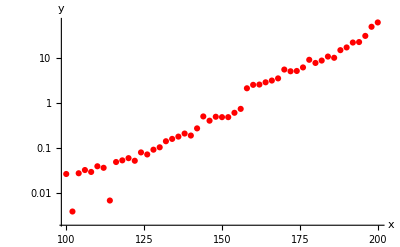

```mathematica
data=Transpose[{xValues,executeTimes}];
dataplot=ListLogPlot[data,AxesLabel->{x,y},PlotStyle->Red]
```

```mathematica
exponentialData=Transpose[{xValues,Log[executeTimes]}];
```

```mathematica
expSolution=FindFit[exponentialData, a x+b,{a,b},x]
```

{a→0.083429,b→-12.91}

```mathematica
yExp[x_]=ⅇ^(a x+b)/.expSolution
```

ⅇ^(-12.91+0.083429 x)

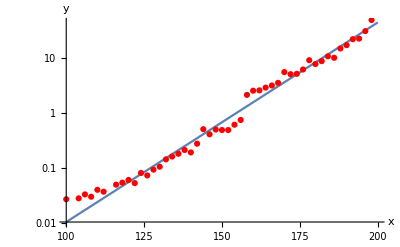

```mathematica
modelplotExp=LogPlot[yExp[x],{x,100,200},AxesLabel->{x,y}];
Show[modelplotExp,dataplot]
```

{a→36.795,b→-177.67}

-177.67+36.795 Log[x]

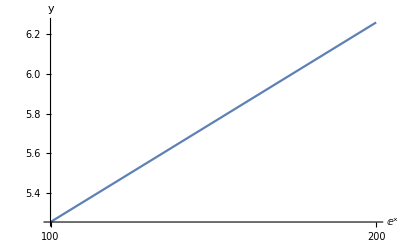

```mathematica
logarithmicData=Transpose[{Log[xValues],executeTimes}];
logSolution=FindFit[logarithmicData,a lnx+b,{a,b},lnx]
yLog[x_]=a Log[x]+b/.logSolution
modelplotLog=LogLinearPlot[y[x],{x,100,200},AxesLabel->{x,y}];
Show[modelplotLog,dataplot]
```

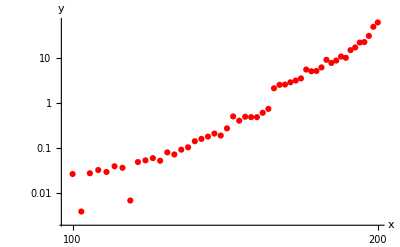

```mathematica
dataplotPow=ListLogLogPlot[data,AxesLabel->{x,y},PlotStyle->Red]
```

{a→12.079,b→-60.678}

4.446×10^-27 x^12.079

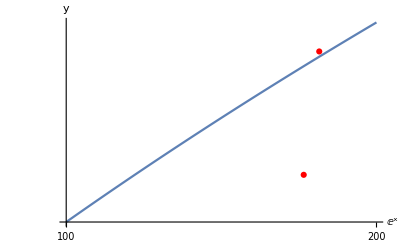

```mathematica
dataPow=Transpose[{Log[xValues],Log[executeTimes]}];
solutionPow=FindFit[dataPow,a lnx+b,{a,b},lnx]
yPow[x_]=ⅇ^b x^a/.solutionPow
modelplotPow=LogLogPlot[y[x],{x,100,200},AxesLabel->{x,y}];
Show[modelplotPow,dataplotPow]
```

```mathematica
N[ⅇ,50]
```

2.7182818284590452353602874713526624977572470937

```mathematica
test="hejsa";
t1=ToCharacterCode[test];
t2=256^(Range[StringLength[test]]-1);
testCode=t1.t2
enc=PowerMod[testCode,1651,10000049000057];
dTest=PowerMod[1651,-1,10000038000036];
PowerMod[enc,dTest,10000049000057]
```

418548180328

418548180328